# Vernier LabQuest 2

## Wolfram Language Interface

#### Load and Connect

This loads the “LabQuest2” package:

```mathematica
Needs["LabQuest2`"]
```

This sets up the connection to a LabQuest 2 device. An arbitrary number of devices can be supported here, which may be useful in a classroom (teacher+students) context:

```mathematica
labquest2=InstallLabQuest2["140.177.208.85"]
```

LabQuest2Object[…]

#### Examine Properties and Status

The LabQuest2Object has several properties for querying status, retrieving data, and controlling the device:

```mathematica
labquest2["Properties"]
```

{Status,Start,Stop,Sets,Set,Views,Columns,Plot}

The “Status” property retrieves the current device status. At the moment the full data is returned as a Dataset:

```mathematica
status=labquest2["Status"]
```

Dataset[<>]

This is a look into the collection of experiments that have been run on the device:

```mathematica
sets=labquest2["Sets"]
```

Dataset[<>]

More detailed device information, specifically for plotting meta-information (range, title, plot styles):

```mathematica
views=labquest2["Views"]
```

Dataset[<>]

Detailed information about “Columns” including data type and units (time stamps appears to be in UNIX time):

```mathematica
columns=labquest2["Columns"]
```

Dataset[<>]

#### Retrieve Data and Analyze

Retrieve the collected data for a particular set (as found with the “Sets” property):

```mathematica
data=labquest2[{"Set","286"}]
```

Dataset[<>]

Plot the data for a given set (currently only works with a single sensor):

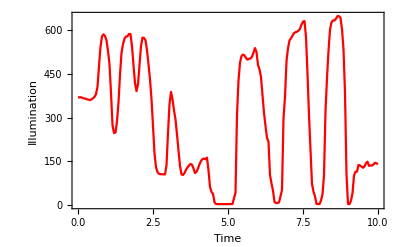

```mathematica
data=labquest2[{"Plot","286"}]
```

#### Starting and Stopping Experiments

Start a measurement run:

```mathematica
labquest2["Start"]
```

{result→1}

Stop a measurement run, before the listed end time point:

```mathematica
labquest2["Stop"]
```

{result→0}